## Proposition 1: Valerie is a Totally Awesome Person

## Proof:

### Part 1

In this exercise, we define ♝ to be the set of all people that have ever lived and ⌚ to be the set of everything that exists now. 

Let Valerie ∈ ♝ ∪ ⌚ be denoted by 🐺. 

To be a member of the set of all totally awesome things denoted by α_τ, an element of the set ♝, denoted here by ♘, must be a satisfy the following conditions:

	(1) ♘ ∈ Γ,  where Γ = { μ | μ does cool things }
	(2) ♘ ∈ ℙ, where ℙ  = { ψ | ψ has a great personality }
	(3) ♘ ∈ 
	(4) [♘]_N = { δ  | δ →^N any β,  β ⊂ ♝,|β|>0 } where N is the “nice” relation (discussed in part 2)   
	(5) [♘]_C = { γ  | γ →^C any ν,  ν ⊂ ♝,|ν|>0 } where C is the “care” relation (discussed in part 3)

### Part 2

The “nice” relation is an interaction between two nodes where an action of “niceness” can be visualized as the directed edge between two nodes.

```mathematica
effected=Table["Gatton Student "<>ToString[i],{i,1,120}];
```

```mathematica
rand=Table["Random person "<>ToString[i],{i,1,10000}];
```

```mathematica
grouped=Flatten[Table[Table[effected[[i]]->RandomChoice[Union[rand,effected]],{i,Length[effected]}],{15}]];
```

```mathematica
p=Union[("Valerie"->#)&/@effected,grouped];
```

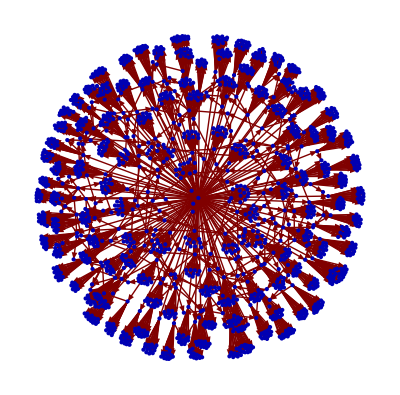

```mathematica
GraphPlot[p,VertexLabeling->Tooltip,DirectedEdges->True]
```

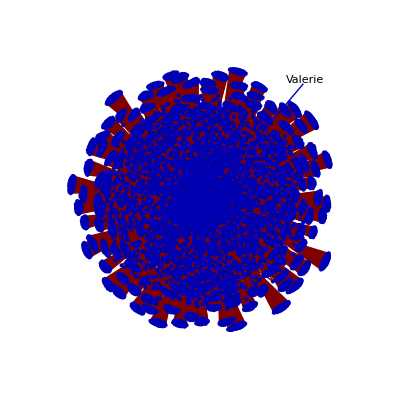

```mathematica
VectorPlot
```